## Exponential Distribution

```mathematica
$Assumptions=λ>0&&n>0&&i>0&&i<1+n;
cdf[x_]:=1-Exp[-λ*x];
pdf[x_]:=λ*Exp[-λ*x];
(*PDF of the i-th Order Statistic*)pdfOrderStatistic[x_,i_,n_]:=n!/(Factorial[i-1]*Factorial[n-i])*cdf[x]^(i-1)*(1-cdf[x])^(n-i)*pdf[x];
(*Expected Value of the i-th Order Statistic*)expectedValueOrderStatistic[i_,n_]:=Integrate[x*pdfOrderStatistic[x,i,n],{x,0,Infinity}];
(* Calculate the expected value for the i-th order statistic *)
ev = expectedValueOrderStatistic[i, n]
```

(HarmonicNumber[n]-HarmonicNumber[-i+n])/λ

```mathematica
Series[HarmonicNumber[n]/λ,{n,∞,1}]
```

(EulerGamma+Log[n])/λ+1/(2 λ n)+O[1/n]^2

```mathematica
small=(EulerGamma+Log[n])/λ;
large=(EulerGamma+Log[c*n])/λ;
```

```mathematica
FullSimplify[large/small,c>1]
```

1+Log[c]/(EulerGamma+Log[n])

```mathematica
FullSimplify[(large-small)/small,c>1]
```

Log[c]/(EulerGamma+Log[n])

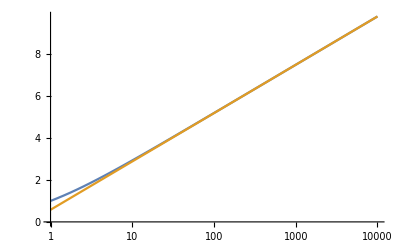

```mathematica
λ=1;
LogLinearPlot[{HarmonicNumber[n]/λ,(EulerGamma+Log[n])/λ},{n,1,10000}]
Clear[λ]
```

## Pareto Distribution

```mathematica
$Assumptions=α>0&&xm>0&&i>0&&i<1+n;
cdf[x_]:=1-(xm/x)^α;
pdf[x_]:=(α*xm^α)/x^(α+1);
(*PDF of the i-th Order Statistic*)pdfOrderStatistic[x_,i_,n_]:=n!/(Factorial[i-1]*Factorial[n-i])*cdf[x]^(i-1)*(1-cdf[x])^(n-i)*pdf[x];
(*Expected Value of the i-th Order Statistic*)expectedValueOrderStatistic[i_,n_]:=Integrate[x*pdfOrderStatistic[x,i,n],{x,xm,Infinity}];
(* Calculate the expected value for the i-th order statistic *)
ev = expectedValueOrderStatistic[i, n]
```

ConditionalExpression[(π xm^(1+(-1+i-n) α+(1-i+n) α) Csc[i π] n! Gamma[1-i+n-1/α])/((-1+i)! (-i+n)! Gamma[1-i] Gamma[1+n-1/α]), 1+i α<(1+n) α]

```mathematica
FullSimplify[(π xm^(1+(-1+i-n) α+(1-i+n) α) Csc[i π] n! Gamma[1-i+n-1/α])/((-1+i)! (-i+n)! Gamma[1-i] Gamma[1+n-1/α])]
```

(xm n! Gamma[1-i+n-1/α])/(Gamma[1-i+n] Gamma[1+n-1/α])

```mathematica
FullSimplify[(xm n! Gamma[1-1/α])/(Gamma[1] Gamma[1+n-1/α])]
```

(xm n! Gamma[(-1+α)/α])/Gamma[1+n-1/α]

```mathematica
Series[(xm n! Gamma[(-1+α)/α])/Gamma[1+n-1/α],{n,∞,1}]
```

n^(-1+1/α) (xm Gamma[(-1+α)/α] n+(xm (-1+α) Gamma[(-1+α)/α])/(2 α^2)-(xm (-3+10 α-9 α^2+2 α^3) Gamma[(-1+α)/α])/(24 α^4 n)+O[1/n]^2)

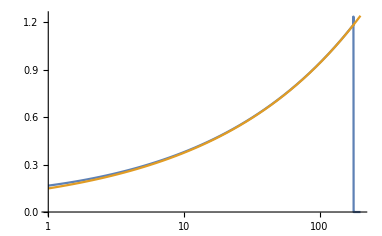

0.148919

```mathematica
α=2.5;
xm=0.1;
LogLinearPlot[{(xm n! Gamma[(-1+α)/α])/Gamma[1+n-1/α],n^(1/α) xm Gamma[(-1+α)/α]},{n,1,200}]
xm Gamma[(-1+α)/α]
Clear[α,xm]
```

```mathematica
FullSimplify[n^(-1+1/α)(xm Gamma[(-1+α)/α] n)]
```

n^(1/α) xm Gamma[(-1+α)/α]

```mathematica
FullSimplify[(c*n)^(1/α)/(n)^(1/α),c>1]
```

c^(1/α)

```mathematica
FullSimplify[(c*n)^(1/α) xm Gamma[(-1+α)/α]/((n)^(1/α) xm Gamma[(-1+α)/α]),c>1]
```

c^(1/α)

```mathematica
FullSimplify[((c*n)^(1/α) xm Gamma[(-1+α)/α]-(n)^(1/α) xm Gamma[(-1+α)/α])/((n)^(1/α) xm Gamma[(-1+α)/α]),c>1]
```

-1+c^(1/α)